```mathematica
<< MASStoolbox`
<< MASStoolbox`Style`
<< XML`
SetDirectory[NotebookDirectory[]];
<< util`
bigg2equilibrator = Import["../data/bigg2equilibratorViaKEGG.m.gz"];
```

# iAB-RBC-238

## SBML2MODEL

### Import model from SBML and translate to MASSmodel

#### Flux Bounds

```mathematica
getReferenceFluxesAndBoundsFromXML[path_String]:=Block[{tmp,tmp2,tmp3,tmp4},
tmp=Import[path,"Text"];
tmp2=StringCases[tmp,RegularExpression["(?s)listOfReactions.+"]];
tmp3=Flatten[StringSplit[tmp2,RegularExpression["<reaction id="]][[1]][[2;;]]];
tmp4=StringCases[#,RegularExpression["(?s)^(\"R_.+?\").+\"LOWER_BOUND\"\\s*?value=\"([-e\\d\\.]+)\".+?\"UPPER_BOUND\"\\s*?value=\"([-e\\d\\.]+)\".+?\"FLUX_VALUE\"\\s*?value=\"(.+?)\""]:>N[{"$1"->{ToExpression@StringReplace["$2","e"->"*10^"],ToExpression@StringReplace["$3","e"->"*10^"],ToExpression@StringReplace["$4","e"->"*10^"]}}]]&/@tmp3;
Flatten[tmp4]/.s_String:>StringReplace[s,{"\""->""}]
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
iABrefBounds=#[[1]]->#[[2,1;;2]]&/@(getReferenceFluxesAndBoundsFromXML["../data/iAB-RBC-238/1752-0509-5-110-s5.xml.gz"]//.s_String:>StringReplace[s,biggCommonStringReplacements]);
```

#### GPR

```mathematica
protAssoc=Flatten[Thread[#[[1]]->(If[StringMatchQ[#,RegularExpression[".*\\+.*"]],proteinComplex[Sequence@@(protein/@StringSplit[#,RegularExpression["\\s*\\+\\s*"]])],protein[#]]&/@StringSplit[#[[2]],RegularExpression["\\s*,\\s*"]])]&/@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[1]][[2;;,{1,-5}]],{_,"''"}]];
```

```mathematica
protAssoc//Length
protAssoc//Union//Length
```

784

777

```mathematica
protAssoc=Union[protAssoc];
```

#### Elemental composition

```mathematica
bigg2inchi=Import["/Users/niko/work/Code/MathematicaRepo/MASStoolbox/Models/Mappings/bigg2inchi.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
elementalComposition=str2mass[#[[1]]]->formula2elementalComposition[#[[4]]]&/@DeleteCases[Import["../data/iAB-RBC-238/1752-0509-5-110-s4.xls.gz"][[2]],{"","","",""}][[2;;]];
```

#### Build model

```mathematica
SetDirectory[NotebookDirectory[]];
rbcReactions=(sbml2model["../data/iAB-RBC-238/1752-0509-5-110-s5.xml.gz", Method->"Light"])["Reactions"]//.s_String:>StringReplace[s,biggCommonStringReplacements];
correctRxnsAndBounds=Table[
	bnds=getID[rxn]/.iABrefBounds;
	If[!reversibleQ[rxn],Switch[bnds,{a_/;a<0,b_/;b<=0},Reverse@rxn->Abs[Reverse[bnds]],_,rxn->(bnds)],rxn->(bnds)]
	,{rxn,rbcReactions}
];
rbc=constructModel[correctRxnsAndBounds[[All,1]],Constraints->(getID[#[[1]]]->#[[2]]&/@correctRxnsAndBounds),Ignore->{m["h",_],m["h2o",_]},"ReorderStoichiometry"->False];
updateNotes[rbc,defaultInitializationNotes[]<>"\n This model covers the iAB-RBC-238 reconstruction by Aarash Bordbard."];
setGPR[rbc,protAssoc];
setID[rbc,"iAB-RBC-238"];
setElementalComposition[rbc,elementalComposition];
dg=Quiet[calcDeltaG[rbc["Reactions"],bigg2equilibrator,is->0.25 Mole Liter^-1,pH->7.3],{calcDeltaG::missingPseudoisomerData}];
Print["Proportion of reactions without thermodynamic information."];
Count[dg,r_Rule/;r[[2]]===Undefined]/N@Length[rbcᵀ]
keq=dG2keq[DeleteCases[dg,r_Rule/;r[[2]]===Undefined]];
keq=adjustUnits[keq,rbc,DefaultAmountUnit->Millimole];
updateParameters[rbc,keq]
```

Proportion of reactions without thermodynamic information.

0.343284

```mathematica
DeleteCases[stripUnits@dg[[All,2]],Undefined]//Length
```

308

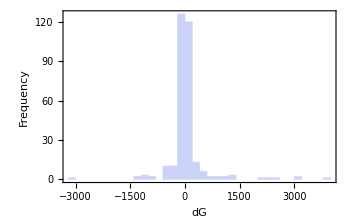

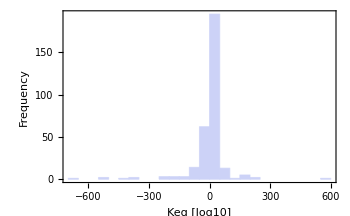

```mathematica
Histogram[DeleteCases[stripUnits@dg[[All,2]],Undefined],FrameLabel->{"dG","Frequency"}]
Histogram[Log[10,stripUnits@FilterRules[rbc["Parameters"],_Keq][[All,2]]],FrameLabel->{"Keq [log10]","Frequency"}]
```

```mathematica
stoichiometricallyConsistentQ[rbc]
```

True

```mathematica
elementallyBalancedQ@rbc
```

True

```mathematica
rbc["Fluxes"]//Length
rbc["Fluxes"]//Union//Length
rbc["Proteins"]//Union//Length
```

469

469

347

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238.m.gz",rbc]
```

../models/iAB-RBC-238/iAB-RBC-238.m.gz

```mathematica
getNotes@rbc
```

Model constructed on Wed 24 Oct 2012 14:32:06 by niko on staphylococcus.ucsd.edu using Mathematica 8.0 for Mac OS X x86 (64-bit) (October 5, 2011) at the following geodetic location: latitude 32.88; longitude -117.24
 This model covers the iAB-RBC-238 reconstruction by Aarash Bordbard.

### Visualize model

```mathematica
(*currencyMets=annotateCurrencyMetabolites[getReactions@rbc];
SetDirectory[NotebookDirectory[]];
Export["../Data/iAB-RBC-238/currencyMetsRBC.m.gz",currencyMets];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
currencyMets=Import["../Data/iAB-RBC-238/currencyMetsRBC.m.gz"];
```

```mathematica
net=pathwaytize[DeleteCases[reactions2bipartite[getReactions[rbc],AliasingRules->currencyMets],r_Rule/;MemberQ[r,m_metabolite/;StringMatchQ[getID[m],RegularExpression[".*\\$.*"]],∞]],10,Method->"Remove"];
(*net=DeleteCases[reactions2bipartite[getReactions[rbc],AliasingRules->currencyMets],r_Rule/;MemberQ[r,m_metabolite/;StringMatchQ[getID[m],RegularExpression[".*\\$.*"]],∞]];*)
connComponents=ConnectedComponents@Graph[Union[(Rule@@Sort[List@@#]&/@net)]/.r_Rule:>UndirectedEdge@@r];
nets=Cases[net,r_Rule/;MemberQ[#,Alternatives@@r]]&/@Sort[connComponents,Length[#1]>Length[#2]&];
transp=Cases[Union@Cases[nets,r_Rule/;MemberQ[r,metabolite[_,"e"],∞],∞],_String,2];
```

```mathematica
SlideView[visualizePathways[DeleteCases[#,r_Rule/;MemberQ[transp,r[[1]]]||MemberQ[transp,r[[2]]]||MemberQ[r,s_String/;StringMatchQ[s,RegularExpression[".*DM_.*"]]||StringMatchQ[s,RegularExpression[".*sink_.*"]],∞]],
PlotFunction->LayeredGraphPlot,ImageSize->1200,EdgeRenderingFunction->({If[EuclideanDistance[#1[[1]],#1[[-1]]]>5,Unevaluated[Sequence[Gray,Dotted]],Black],Arrow[#1,0.1]}&)]&/@nets[[1;;2]]]
```

### Visualize GPRs

```mathematica
SlideView[visualizeGPR[#]&/@gpr2graphs[rbc["GPR"]],AppearanceElements->All]
```

## Translate SB2 book models to iAB-RBC-238

```mathematica
sb2MetsToiAB={metabolite["glu",comp_]:>metabolite["glc-D",comp],metabolite["gap",comp_]:>metabolite["g3p",comp],metabolite["phos",comp_]:>metabolite["pi",comp],metabolite["pg13",comp_]:>metabolite["13dpg",comp],metabolite["pg3",comp_]:>metabolite["3pg",comp],metabolite["pg2",comp_]:>metabolite["2pg",comp],metabolite["lac",comp_]:>metabolite["lac-L",comp],metabolite["gl6p",comp_]:>metabolite["6pgl",comp],metabolite["go6p",comp_]:>metabolite["6pgc",comp],metabolite["ru5p",comp_]:>metabolite["ru5p-D",comp],metabolite["x5p",comp_]:>metabolite["xu5p-D",comp],metabolite["gssg",comp_]:>metabolite["gthox",comp],metabolite["gsh",comp_]:>metabolite["gthrd",comp],metabolite["ado",comp_]:>metabolite["adn",comp],metabolite["ino",comp_]:>metabolite["ins",comp],metabolite["hyp",comp_]:>metabolite["hxan",comp]};
```

### Glycolysis

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../models/SB2/glycolysis.m.gz"];
```

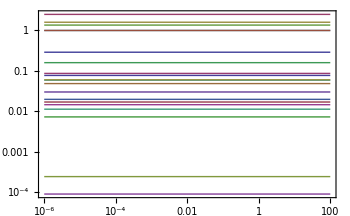

```mathematica
plotSimulation[simulate[glycolysis,{t,0,100}][[1]]]/.m:$MASS$speciesPattern:>ToString[m]
```

```mathematica
sb2ToiAB={"vhk"->"HEX1","vpgi"->"PGI","vpfk"->"PFK","vtpi"->"TPI","vald"->"FBA",
"vgapdh"->"GAPD","vpgk"->"PGK","vpglm"->"PGM","veno"->"ENO","vpk"->"PYK",
"vldh"->"LDH_L","vamp"->Missing["NotAvailable"],"vapk"->"ADK1",
"vpyr"->Missing["NotAvailable"],"vlac"->Missing["NotAvailable"],
"vatp"->Missing["NotAvailable"],"vnadh"->Missing["NotAvailable"],
"vgluin"->Missing["NotAvailable"],"vampin"->Missing["NotAvailable"],"vh"->Missing["NotAvailable"],"vh2o"->Missing["NotAvailable"]
};
```

```mathematica
TableForm[{Cases[glycolysis["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(atp^c+(glc-D)^c⇌adp^c+g6p^c+h^c)^vhk | (atp^c+(glc-D)^c→adp^c+g6p^c+h^c)^HEX1
(g6p^c⇌f6p^c)^vpgi | (g6p^c⇌f6p^c)^PGI
(atp^c+f6p^c⇌adp^c+fdp^c+h^c)^vpfk | (atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK
(dhap^c⇌g3p^c)^vtpi | (dhap^c⇌g3p^c)^TPI
(fdp^c⇌dhap^c+g3p^c)^vald | (fdp^c⇌dhap^c+g3p^c)^FBA
(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^vgapdh | (g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD
((13dpg)^c+adp^c⇌(3pg)^c+atp^c)^vpgk | ((3pg)^c+atp^c⇌(13dpg)^c+adp^c)^PGK
((3pg)^c⇌(2pg)^c)^vpglm | ((2pg)^c⇌(3pg)^c)^PGM
((2pg)^c⇌h2o^c+pep^c)^veno | ((2pg)^c⇌h2o^c+pep^c)^ENO
(adp^c+h^c+pep^c⇌atp^c+pyr^c)^vpk | (adp^c+h^c+pep^c→atp^c+pyr^c)^PYK
(h^c+nadh^c+pyr^c⇌(lac-L)^c+nad^c)^vldh | ((lac-L)^c+nad^c⇌h^c+nadh^c+pyr^c)^LDH_L
(amp^c⇌∅)^vamp | —
(2 adp^c⇌amp^c+atp^c)^vapk | (amp^c+atp^c⇌2 adp^c)^ADK1
(pyr^c⇌∅)^vpyr | —
((lac-L)^c⇌∅)^vlac | —
(atp^c+h2o^c⇌adp^c+h^c+pi^c)^vatp | —
(nadh^c⇌h^c+nad^c)^vnadh | —
(∅⇌(glc-D)^c)^vgluin | —
(∅⇌amp^c)^vampin | —
(h^c⇌∅)^vh | —
(h2o^c⇌∅)^vh2o | —

```mathematica
sb2ToiABnew={"vhk"->"HEX1","vpgi"->"PGI","vpfk"->"PFK","vtpi"->"TPI","vald"->"FBA","vgapdh"->"GAPD","vpgk"->"PGK","vpglm"->"PGM","veno"->"ENO","vpk"->"PYK",
"vldh"->"LDH_L","vapk"->"ADK1","vpyr"->"Sink_pyr_c","vlac"->"Sink_lac-L_c","vatp"->"ATP_hydrolysis","vnadh"->"NADH_oxidation","vgluin"->"Sink_glc-D_c","vh"->"Sink_h_c","vh2o"->"Sink_h2o_c"};
```

```mathematica
iABglycolysis=subModel[rbc,DeleteCases[getID/@glycolysis["Fluxes"]/.sb2ToiAB,_Missing]];
setUnitChecking[iABglycolysis,True]
setID[iABglycolysis,"iAB-RBC-238-Glycolysis"];
setIgnore[iABglycolysis,{m["h",_],m["h2o",_]}]
iABglycolysis=addSinks[iABglycolysis,{pyr^c,(lac-L)^c,(glc-D)^c,h^c,h2o^c}];
iABglycolysis=addReactions[iABglycolysis,{Overscript[atp^c+h2o^c⇌adp^c+h^c+pi^c, ATP_hydrolysis],Overscript[nadh^c⇌h^c+nad^c, NADH_oxidation]}];
setInitialConditions[iABglycolysis,Join[
#[[1]]->#[[2]]Millimole Liter^-1&/@{(glc-D)^c->1.,g6p^c->0.0486,f6p^c->0.0198,fdp^c->0.0146,dhap^c->0.16,g3p^c->0.00728,(13dpg)^c->0.000243,(3pg)^c->0.0773,(2pg)^c->0.0113,pep^c->0.017,pyr^c->0.060301,(lac-L)^c->1.36,nad^c->0.0589,nadh^c->0.0301,amp^c->0.08672812499999999,adp^c->0.29,atp^c->1.6,pi^c->2.5,h^c->0.00008997573444801929,h2o^c->1.},
#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@{"HEX1"->1.12,"PGI"->1.12,"PFK"->1.12,"TPI"->1.12,"FBA"->1.12,"GAPD"->2.24,"PGK"->-2.24,"PGM"->-2.24,"ENO"->2.24,"PYK"->2.24,"LDH_L"->-2.016,"ADK1"->0.,"Sink_pyr[c]"->0.22400000000000003,"Sink_lac-L[c]"->2.016,"ATP_hydrolysis"->2.24,
"NADH_oxidation"->0.22400000000000003,"Sink_glc-D[c]"->-1.12,"Sink_h[c]"->2.688,"Sink_h2o[c]"->0.}
]];
xtrnalConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{pyr^Xt->0.06,amp^Xt->1,h^Xt->0.00006309573444801929,metabolite[_,"Xt"]->1};
setParameters[iABglycolysis,Join[{parameter["Volume", "c"] -> Liter, Keq["HEX1"] -> 850, Keq["PGI"] -> 0.41, Keq["PFK"] -> 310, Keq["TPI"] -> 0.05714285714285714, Keq["FBA"] -> 0.082, 
  Keq["GAPD"] -> 0.0179, Keq["PGK"] -> 1/1800, Keq["PGM"] -> 6.8, Keq["ENO"] -> 1.6949152542372883, Keq["PYK"] -> 363000, Keq["LDH_L"] -> 1/26300, Keq["ADK1"] -> 0.6060606060606061, 
  Keq["Sink_pyr[c]"] -> 1., Keq["Sink_lac-L[c]"] -> 1., Keq["ATP_hydrolysis"] -> Infinity, Keq["NADH_oxidation"] -> Infinity, Keq["Sink_glc-D[c]"] -> 0, Keq["Sink_h[c]"] -> 1., 
  Keq["Sink_h2o[c]"] -> 1.},xtrnalConc]];

perc=calcPERC[iABglycolysis,"AtEquilibriumDefault"->1];
updateParameters[iABglycolysis,perc];
updateNotes[iABglycolysis,defaultInitializationNotes[]<>"\n This model is a translation of the glycolysis model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbard."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz",iABglycolysis]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed.

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::atequilibrium: Reaction "ADK1" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 1 (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::ZeroKeq: The equilibrium constant K StyleBox[ of reaction "Sink_glc-D[c]" is zero, the PERC of the reverse rate constant k_StyleBox[ will be calculated.

calcPERC::atequilibrium: Reaction "Sink_h2o[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 1 (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed.

../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz

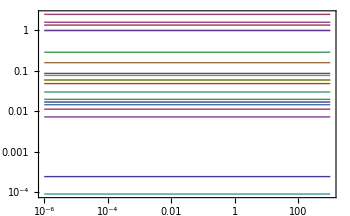

```mathematica
{concSol,fluxSol}=simulate[iABglycolysis,{t,0,1000}];
plotSimulation[concSol]/.m_metabolite:>getID[m]
```

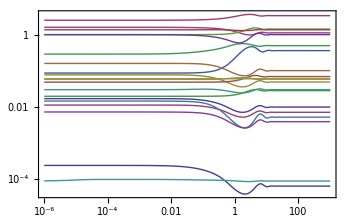

```mathematica
{concSol,fluxSol}=simulate[iABglycolysis,{t,0,1000},Parameters->{Subscript[k, ATP_hydrolysis]^⟶->2 Hour^-1}];
plotSimulation[concSol]/.m_metabolite:>getID[m]
```

### Pentose phosphate pathway

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
ppp=Import["../models/SB2/ppp.m.gz"];
```

```mathematica
sb2ToiAB={"vg6pdh"->"G6PDH2r","vpglase"->"PGL","vgl6pdh"->"GND","vr5pe"->"RPE","vr5pi"->"RPI","vtki"->"TKT1","vtkii"->"TKT2","vtala"->"TALA","vgssgr"->"GTHO","vgshr"->"GTHP"}
```

{vg6pdh→G6PDH2r,vpglase→PGL,vgl6pdh→GND,vr5pe→RPE,vr5pi→RPI,vtki→TKT1,vtkii→TKT2,vtala→TALA,vgssgr→GTHO,vgshr→GTHP}

```mathematica
ppp["Reactions"]
```

{(g6p^c+nadp^c⇌gl6p^c+h^c+nadph^c)^vg6pdh,(gl6p^c+h2o^c⇌go6p^c+h^c)^vpglase,(go6p^c+nadp^c⇌co2^c+nadph^c+ru5p^c)^vgl6pdh,(ru5p^c⇌x5p^c)^vr5pe,(ru5p^c⇌r5p^c)^vr5pi,(r5p^c+x5p^c⇌gap^c+s7p^c)^vtki,(e4p^c+x5p^c⇌f6p^c+gap^c)^vtkii,(gap^c+s7p^c⇌e4p^c+f6p^c)^vtala,(gssg^c+h^c+nadph^c⇌2 gsh^c+nadp^c)^vgssgr,(2 gsh^c⇌gssg^c+2 h^c)^vgshr,(co2^c⇌∅)^vco2,(g6p^c⇌∅)^EX_g6p_c,(f6p^c⇌∅)^EX_f6p_c,(r5p^c⇌∅)^EX_r5p_c,(h^c⇌∅)^EX_h_c,(h2o^c⇌∅)^EX_h2o_c,(gap^c⇌∅)^EX_gap_c}

```mathematica
TableForm[{Cases[ppp["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^vg6pdh | (g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r
((6pgl)^c+h2o^c⇌(6pgc)^c+h^c)^vpglase | ((6pgl)^c+h2o^c→(6pgc)^c+h^c)^PGL
((6pgc)^c+nadp^c⇌co2^c+nadph^c+(ru5p-D)^c)^vgl6pdh | ((6pgc)^c+nadp^c→co2^c+nadph^c+(ru5p-D)^c)^GND
((ru5p-D)^c⇌(xu5p-D)^c)^vr5pe | ((ru5p-D)^c⇌(xu5p-D)^c)^RPE
((ru5p-D)^c⇌r5p^c)^vr5pi | (r5p^c⇌(ru5p-D)^c)^RPI
(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^vtki | (r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1
(e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^vtkii | (e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^TKT2
(g3p^c+s7p^c⇌e4p^c+f6p^c)^vtala | (g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA
(gthox^c+h^c+nadph^c⇌2 gthrd^c+nadp^c)^vgssgr | (gthox^c+h^c+nadph^c→2 gthrd^c+nadp^c)^GTHO
(2 gthrd^c⇌gthox^c+2 h^c)^vgshr | (2 gthrd^c+h2o2^c→gthox^c+2 h2o^c)^GTHP

```mathematica
ppp["InitialConditions"]
```

{g6p^c→0.0486 Millimole Liter^-1,f6p^c→0.0198 Millimole Liter^-1,gap^c→0.00728 Millimole Liter^-1,gl6p^c→0.00175424 Millimole Liter^-1,go6p^c→0.0374753 Millimole Liter^-1,ru5p^c→0.00493679 Millimole Liter^-1,x5p^c→0.0147842 Millimole Liter^-1,r5p^c→0.0126689 Millimole Liter^-1,s7p^c→0.023988 Millimole Liter^-1,e4p^c→0.00507507 Millimole Liter^-1,nadp^c→0.0002 Millimole Liter^-1,nadph^c→0.0658 Millimole Liter^-1,gsh^c→3.2 Millimole Liter^-1,gssg^c→0.12 Millimole Liter^-1,co2^c→1. Millimole Liter^-1,h^c→0.0000714957 Millimole Liter^-1,h2o^c→0.999998 Millimole Liter^-1,v_vg6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vpglase→0.21 Millimole Hour^-1 Liter^-1,v_vgl6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vr5pe→0.133333 Millimole Hour^-1 Liter^-1,v_vr5pi→0.0766667 Millimole Hour^-1 Liter^-1,v_vtki→0.0666667 Millimole Hour^-1 Liter^-1,v_vtkii→0.0666667 Millimole Hour^-1 Liter^-1,v_vtala→0.0666667 Millimole Hour^-1 Liter^-1,v_vgssgr→0.42 Millimole Hour^-1 Liter^-1,v_vgshr→0.42 Millimole Hour^-1 Liter^-1,v_vco2→0.21 Millimole Hour^-1 Liter^-1,v_EX_g6p_c→-0.21 Millimole Hour^-1 Liter^-1,v_EX_f6p_c→0.133333 Millimole Hour^-1 Liter^-1,v_EX_r5p_c→0.01 Millimole Hour^-1 Liter^-1,v_EX_h_c→0.84 Millimole Hour^-1 Liter^-1,v_EX_h2o_c→-0.21 Millimole Hour^-1 Liter^-1,v_EX_gap_c→0.0666667 Millimole Hour^-1 Liter^-1}

```mathematica
FilterRules[ppp["Parameters"],_metabolite]
```

{h^Xt→0.0000630957 Millimole Liter^-1,metabolite[_,Xt]→Millimole Liter^-1}

```mathematica
ppp["Parameters"]
```

{Volume_c→Liter,K_EX_r5p_c→∞,K_EX_h_c→1,K_EX_h2o_c→1,K_EX_g6p_c→1,K_EX_gap_c→∞,K_EX_f6p_c→∞,K_vg6pdh→1000,K_vpglase→1000,K_vgl6pdh→1000 Millimole Liter^-1,K_vr5pe→3,K_vr5pi→2.57,K_vtki→1.2,K_vtkii→10.3,K_vtala→1.05,K_vgssgr→100 Millimole Liter^-1,K_vgshr→2 Liter Millimole^-1,K_vco2→1,h^Xt→0.0000630957 Millimole Liter^-1,k_vg6pdh^⟶→21864.6 Liter Hour^-1 Millimole^-1,k_vpglase^⟶→122.323 Hour^-1,k_vgl6pdh^⟶→29287.8 Liter Hour^-1 Millimole^-1,k_vr5pe^⟶→15281.8 Hour^-1,k_vr5pi^⟶→10584.6 Hour^-1,k_vtki^⟶→1595.93 Liter Hour^-1 Millimole^-1,k_vtkii^⟶→1092.25 Liter Hour^-1 Millimole^-1,k_vtala^⟶→844.617 Liter Hour^-1 Millimole^-1,k_vgssgr^⟶→53.3298 Liter Hour^-1 Millimole^-1,k_vgshr^⟶→0.0412574 Liter Hour^-1 Millimole^-1,k_vco2^⟶→100000. Hour^-1,k_EX_g6p_c^⟶→0.220727 Hour^-1,k_EX_f6p_c^⟶→6.73401 Hour^-1,k_EX_r5p_c^⟶→0.789332 Hour^-1,k_EX_h_c^⟶→100000. Hour^-1,k_EX_h2o_c^⟶→100000. Hour^-1,k_EX_gap_c^⟶→9.15751 Hour^-1,metabolite[_,Xt]→Millimole Liter^-1}

```mathematica
DropUnits@0.0000714957344480193 Millimole Liter^-1
```

0.0000714957

```mathematica
ppp["Fluxes"]
```

{v_vg6pdh,v_vpglase,v_vgl6pdh,v_vr5pe,v_vr5pi,v_vtki,v_vtkii,v_vtala,v_vgssgr,v_vgshr,v_vco2,v_EX_g6p_c,v_EX_f6p_c,v_EX_r5p_c,v_EX_h_c,v_EX_h2o_c,v_EX_gap_c}

```mathematica
FilterRules[ppp["InitialConditions"],_v]
```

{v_vg6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vpglase→0.21 Millimole Hour^-1 Liter^-1,v_vgl6pdh→0.21 Millimole Hour^-1 Liter^-1,v_vr5pe→0.133333 Millimole Hour^-1 Liter^-1,v_vr5pi→0.0766667 Millimole Hour^-1 Liter^-1,v_vtki→0.0666667 Millimole Hour^-1 Liter^-1,v_vtkii→0.0666667 Millimole Hour^-1 Liter^-1,v_vtala→0.0666667 Millimole Hour^-1 Liter^-1,v_vgssgr→0.42 Millimole Hour^-1 Liter^-1,v_vgshr→0.42 Millimole Hour^-1 Liter^-1,v_vco2→0.21 Millimole Hour^-1 Liter^-1,v_EX_g6p_c→-0.21 Millimole Hour^-1 Liter^-1,v_EX_f6p_c→0.133333 Millimole Hour^-1 Liter^-1,v_EX_r5p_c→0.01 Millimole Hour^-1 Liter^-1,v_EX_h_c→0.84 Millimole Hour^-1 Liter^-1,v_EX_h2o_c→-0.21 Millimole Hour^-1 Liter^-1,v_EX_gap_c→0.0666667 Millimole Hour^-1 Liter^-1}

```mathematica
Chop[ppp.(ppp["Fluxes"]/.ppp["InitialConditions"])]
```

{0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1,0 Millimole Hour^-1 Liter^-1}

```mathematica
ppp["Reactions"]
```

{(g6p^c+nadp^c⇌gl6p^c+h^c+nadph^c)^vg6pdh,(gl6p^c+h2o^c⇌go6p^c+h^c)^vpglase,(go6p^c+nadp^c⇌co2^c+nadph^c+ru5p^c)^vgl6pdh,(ru5p^c⇌x5p^c)^vr5pe,(ru5p^c⇌r5p^c)^vr5pi,(r5p^c+x5p^c⇌gap^c+s7p^c)^vtki,(e4p^c+x5p^c⇌f6p^c+gap^c)^vtkii,(gap^c+s7p^c⇌e4p^c+f6p^c)^vtala,(gssg^c+h^c+nadph^c⇌2 gsh^c+nadp^c)^vgssgr,(2 gsh^c⇌gssg^c+2 h^c)^vgshr,(co2^c⇌∅)^vco2,(g6p^c⇌∅)^EX_g6p_c,(f6p^c⇌∅)^EX_f6p_c,(r5p^c⇌∅)^EX_r5p_c,(h^c⇌∅)^EX_h_c,(h2o^c⇌∅)^EX_h2o_c,(gap^c⇌∅)^EX_gap_c}

```mathematica
Unit[0.012668936, "Millimole"/"Liter"]
```

0.0126689 Millimole Liter^-1

```mathematica
iABppp=subModel[rbc,ppp["Fluxes"]/.sb2ToiAB];
setUnitChecking[iABppp,True];
setID[iABppp,"iAB-RBC-238-PentosePhosphatePathway"];
setIgnore[iABppp,{m["h",_],m["h2o",_]}];
(*iABppp=addReaction[iABppp,reaction["GSHR", {metabolite["gthrd", "c"]}, {metabolite["h", "c"], metabolite["gthox", "c"]}, {2, 2, 1}, True]]*)(*not in BIGG; should maybe be replaced by glutathione peroxidase GTHP*)
iABppp=addSinks[iABppp,{m["f6p","c"],m["g6p","c"],m["g3p","c"],m["h2o","c"],m["h","c"],m["co2","c"],m["h2o2","c"]}];
(*updateBoundaryConditions[iABppp,{m["h","c"],m["h2o","c"]}];*)

ssFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@{Subscript[v, G6PDH2r]->0.21,Subscript[v, GND]->0.21,Subscript[v, GTHO]->0.42,Subscript[v, GTHP]->0.42,Subscript[v, PGL]->0.21,Subscript[v, RPE]->0.13999999999998636,Subscript[v, RPI]->-0.07000000000005002,Subscript[v, TALA]->0.07000000000005002,Subscript[v, TKT1]->0.07000000000005002,Subscript[v, TKT2]->0.07000000000005002,Subscript[v, Sink_f6p[c]]->0.13999999999999999,Subscript[v, Sink_g6p[c]]->-0.21,Subscript[v, Sink_g3p[c]]->0.06999999999999999,Subscript[v, Sink_h2o[c]]->0.63,Subscript[v, Sink_h[c]]->0.,Subscript[v, Sink_co2[c]]->0.21,Subscript[v, Sink_h2o2[c]]->-0.42};
ssConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{g6p^c->0.0486,f6p^c->0.0198,g3p^c->0.00728,(6pgl)^c->0.001754242723,(6pgc)^c->0.037475258,(ru5p-D)^c->0.0049367903,(xu5p-D)^c->0.014784196,r5p^c->0.012668936,s7p^c->0.023987984,e4p^c->0.0050750696,nadp^c->0.0002,nadph^c->0.0658,gthrd^c->3.2,gthox^c->0.11999999999999966,h^c->0.00006309573444801929,h2o2^c->0.00001,h2o^c->1.99999683,co2^c->1.0000021};
setInitialConditions[iABppp,Join[ssFluxes,ssConc]];
setParameters[iABppp,{parameter["Volume", "c"] -> 1 Liter, Keq["Sink_h[c]"] -> 1, Keq["Sink_h2o[c]"] -> 1, Keq["Sink_g6p[c]"] -> 1, Keq["Sink_g3p[c]"] -> ∞,Keq["Sink_h2o2[c]"] -> 1,
Keq["Sink_co2[c]"] -> 1,Keq["Sink_f6p[c]"] -> ∞, Keq["G6PDH2r"] -> 1000, Keq["PGL"] -> 1000, Keq["GND"] -> 1000, Keq["RPE"] -> 3, Keq["RPI"] -> 1/2.57, 
  Keq["TKT1"] -> 3, Keq["TKT2"] -> 10.3, Keq["TALA"] -> 1.05, Keq["GTHO"] -> 100,Keq["GTHP"] -> ∞(*, Keq["GSHR"] -> 2*),h^Xt->0.00006309573444801929 Millimole Liter^-1, metabolite[_, "Xt"] -> 1 Millimole Liter^-1}];
perc=calcPERC[iABppp]/.Undefined->1000000 Hour^-1;
updateParameters[iABppp,perc];
updateNotes[iABppp,defaultInitializationNotes[]<>"\n This model is a translation of the pentose phosphate pathway model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbard."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz",iABppp]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed.

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::atequilibrium: Reaction "Sink_h[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz

```mathematica
fva[iABppp,{Subscript[v, Sink_f6p[c]]->{-∞,∞},Subscript[v, Sink_g6p[c]]->{-∞,∞},Subscript[v, Sink_g3p[c]]->{-∞,∞},Subscript[v, Sink_h2o[c]]->{-∞,∞},Subscript[v, Sink_h[c]]->{-∞,∞},Subscript[v, Sink_co2[c]]->{-∞,∞},Subscript[v, Sink_h2o2[c]]->{-∞,∞},"G6PDH2r"->{0.21,0.21}}]
```

{v_G6PDH2r→{0.21,0.21},v_GND→{0.21,0.21},v_GTHO→{0.42,0.42},v_GTHP→{0.42,0.42},v_PGL→{0.21,0.21},v_RPE→{0.14,0.14},v_RPI→{-0.07,-0.07},v_TALA→{0.07,0.07},v_TKT1→{0.07,0.07},v_TKT2→{0.07,0.07},v_Sink_f6p[c]→{0.14,0.14},v_Sink_g6p[c]→{-0.21,-0.21},v_Sink_g3p[c]→{0.07,0.07},v_Sink_h2o[c]→{0.63,0.63},v_Sink_h[c]→{0.,0.},v_Sink_co2[c]→{0.21,0.21},v_Sink_h2o2[c]→{-0.42,-0.42}}

```mathematica
fba[iABppp,"GTHP",{Subscript[v, Sink_f6p[c]]->{-∞,∞},Subscript[v, Sink_g6p[c]]->{-∞,∞},Subscript[v, Sink_g3p[c]]->{-∞,∞},Subscript[v, Sink_h2o[c]]->{-∞,∞},Subscript[v, Sink_h[c]]->{-∞,∞},Subscript[v, Sink_co2[c]]->{-∞,∞},Subscript[v, Sink_h2o2[c]]->{-∞,∞},"G6PDH2r"->{0.21,0.21}}]
```

{v_G6PDH2r→0.21,v_GND→0.21,v_GTHO→0.42,v_GTHP→0.42,v_PGL→0.21,v_RPE→0.14,v_RPI→-0.07,v_TALA→0.07,v_TKT1→0.07,v_TKT2→0.07,v_Sink_f6p[c]→0.14,v_Sink_g6p[c]→-0.21,v_Sink_g3p[c]→0.07,v_Sink_h2o[c]→0.63,v_Sink_h[c]→0.,v_Sink_co2[c]→0.21,v_Sink_h2o2[c]→-0.42}

```mathematica
Thread[Rule[iABppp["Species"],iABppp.(iABppp["Fluxes"]/.iABppp["InitialConditions"])]]
```

{(6pgc)^c→0. Millimole Hour^-1 Liter^-1,(6pgl)^c→0. Millimole Hour^-1 Liter^-1,co2^c→0. Millimole Hour^-1 Liter^-1,e4p^c→0. Millimole Hour^-1 Liter^-1,f6p^c→1.00059×10^-13 Millimole Hour^-1 Liter^-1,g3p^c→5.00155×10^-14 Millimole Hour^-1 Liter^-1,gthox^c→0. Millimole Hour^-1 Liter^-1,h^c→0. Millimole Hour^-1 Liter^-1,h2o^c→0. Millimole Hour^-1 Liter^-1,h2o2^c→0. Millimole Hour^-1 Liter^-1,nadp^c→0. Millimole Hour^-1 Liter^-1,nadph^c→0. Millimole Hour^-1 Liter^-1,r5p^c→0. Millimole Hour^-1 Liter^-1,(ru5p-D)^c→-3.63876×10^-14 Millimole Hour^-1 Liter^-1,s7p^c→0. Millimole Hour^-1 Liter^-1,(xu5p-D)^c→-1.13687×10^-13 Millimole Hour^-1 Liter^-1,g6p^c→0. Millimole Hour^-1 Liter^-1,gthrd^c→0. Millimole Hour^-1 Liter^-1}

```mathematica
Sort[perc,stripUnits[#[[2]]]>stripUnits[#2[[2]]]&]
```

{k_Sink_h[c]^⟶→1000000 Hour^-1,k_Sink_co2[c]^⟶→100000. Hour^-1,k_GND^⟶→28018.5 Liter Hour^-1 Millimole^-1,k_G6PDH2r^⟶→21864.6 Liter Hour^-1 Millimole^-1,k_RPE^⟶→16045.9 Hour^-1,k_GTHP^⟶→4101.56 Liter^2 Hour^-1 Millimole^-2,k_RPI^⟶→3760.39 Hour^-1,k_TKT2^⟶→1146.86 Liter Hour^-1 Millimole^-1,k_TALA^⟶→886.848 Liter Hour^-1 Millimole^-1,k_TKT1^⟶→542.261 Liter Hour^-1 Millimole^-1,k_PGL^⟶→119.71 Hour^-1,k_GTHO^⟶→53.1915 Liter Hour^-1 Millimole^-1,k_Sink_g3p[c]^⟶→9.61538 Hour^-1,k_Sink_f6p[c]^⟶→7.07071 Hour^-1,k_Sink_h2o[c]^⟶→0.630002 Hour^-1,k_Sink_h2o2[c]^⟶→0.420004 Hour^-1,k_Sink_g6p[c]^⟶→0.220727 Hour^-1}

```mathematica
findSteadyState[iABppp]//DropUnits
```

{{(6pgc)^c→0.0374753,(6pgl)^c→0.00175424,co2^c→1.,e4p^c→0.00507507,f6p^c→0.0198,g3p^c→0.00728,g6p^c→0.0486,gthox^c→0.12,gthrd^c→3.2,h^c→0.0000630957,h2o^c→2.,h2o2^c→0.00001,nadp^c→0.0002,nadph^c→0.0658,r5p^c→0.0126689,(ru5p-D)^c→0.00493679,s7p^c→0.023988,(xu5p-D)^c→0.0147842},{v_G6PDH2r→0.21,v_GND→0.21,v_GTHO→0.42,v_GTHP→0.42,v_PGL→0.21,v_RPE→0.14,v_RPI→-0.07,v_TALA→0.07,v_TKT1→0.07,v_TKT2→0.07,v_Sink_f6p[c]→0.14,v_Sink_g6p[c]→-0.21,v_Sink_g3p[c]→0.07,v_Sink_h2o[c]→0.63,v_Sink_h[c]→0.,v_Sink_co2[c]→0.21,v_Sink_h2o2[c]→-0.42}}

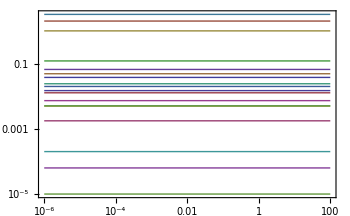

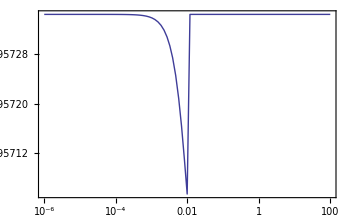

```mathematica
{concSol,fluxSol}=simulate[iABppp,{t,0,100}];
plotSimulation[concSol]
plotSimulation[FilterRules[concSol,m["h",_]],PlotFunction->LogLinearPlot]
```

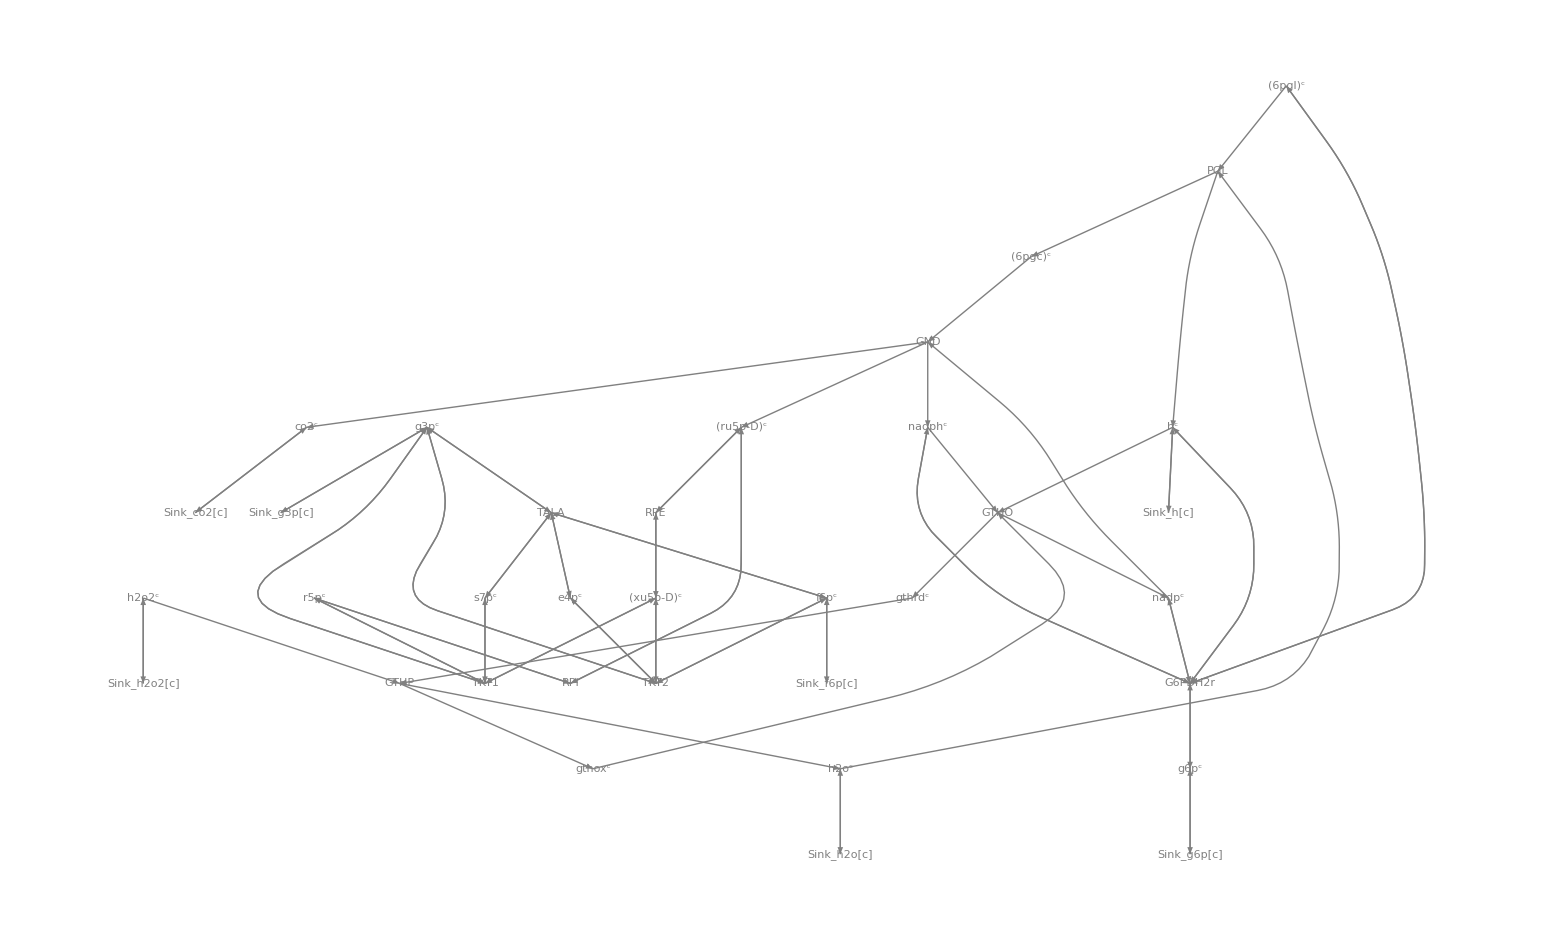

```mathematica
visualizePathways[reactions2bipartite[iABppp["Reactions"]],
DirectedEdges->True,PlotStyle->{GrayLevel[0.5],Arrowheads[.012]},
"MetaboliteRenderingFunction"->({Style[Text[StandardForm@#2,#1],
Background->Opacity[.6,White]]}&),"ReactionRenderingFunction"->({Style[Text[StandardForm@#2,#1],Larger,Background->Opacity[.6,LightGray]]}&),ImageSize->1600,MultiedgeStyle->None]
```

### Nucleotide salvage pathway

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
salvage=Import["../models/SB2/salvage.m.gz"];
```

```mathematica
sb2ToiAB={"vada"->"ADA","vadprt"->"ADPT","vak"->"ADNK1","vampase"->"NTD7","vampda"->"AMPDA","vimpase"->"NTD11","vpnpase"->"PUNP5","vprm"->"PPM","vprppsyn"->"PRPPS"}
```

{vada→ADA,vadprt→ADPT,vak→ADNK1,vampase→NTD7,vampda→AMPDA,vimpase→NTD11,vpnpase→PUNP5,vprm→PPM,vprppsyn→PRPPS}

```mathematica
TableForm[{Cases[salvage["Reactions"],r_reaction/;getID[r]==#[[1]]][[1]],If[MatchQ[#[[2]],_Missing],TraditionalForm@#[[2]],Cases[rbc["Reactions"],r_reaction/;getID[r]==#[[2]]][[1]]]}&/@sb2ToiAB]/.sb2MetsToiAB
```

(adn^c+h2o^c⇌ins^c+nh3^c)^vada | (adn^c+h^c+h2o^c→ins^c+nh4^c)^ADA
(ade^c+h2o^c+prpp^c⇌amp^c+2 pi^c)^vadprt | (ade^c+prpp^c→amp^c+ppi^c)^ADPT
(adn^c+atp^c⇌adp^c+amp^c)^vak | (adn^c+atp^c→adp^c+amp^c+h^c)^ADNK1
(amp^c+h2o^c⇌adn^c+h^c+pi^c)^vampase | (amp^c+h2o^c→adn^c+pi^c)^NTD7
(amp^c+h2o^c⇌imp^c+nh3^c)^vampda | (amp^c+h^c+h2o^c→imp^c+nh4^c)^AMPDA
(h2o^c+imp^c⇌h^c+ins^c+pi^c)^vimpase | (h2o^c+imp^c→ins^c+pi^c)^NTD11
(ins^c+pi^c⇌hxan^c+r1p^c)^vpnpase | (ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5
(r1p^c⇌r5p^c)^vprm | (r1p^c⇌r5p^c)^PPM
(2 atp^c+r5p^c⇌2 adp^c+h^c+prpp^c)^vprppsyn | (atp^c+r5p^c⇌amp^c+h^c+prpp^c)^PRPPS

```mathematica
iABsalvage=subModel[rbc,salvage["Fluxes"]/.sb2ToiAB];
setIgnore[iABsalvage,{m["h","c"],m["h2o","c"]}]
updateUnitChecking[iABsalvage,True]
iABsalvage=addReaction[iABsalvage,Overscript[adp^c+h^c+pi^c⇌atp^c+h2o^c, vatpgen]](*not in BIGG*);
iABsalvage=addSinks[iABsalvage,{m["ade","c"],m["adn","c"],m["hxan","c"],m["ins","c"],m["pi","c"],m["amp","c"],m["h","c"],m["h2o","c"],(*these are new*)m["ppi","c"],m["nh4","c"],m["adp","c"]}];
ssConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{r5p^c->0.00494,ade^c->0.001,adn^c->0.0012,imp^c->0.01,ins^c->0.001,hxan^c->0.002,r1p^c->0.06,prpp^c->0.005,amp^c->0.08672812499999999,adp^c->0.29,atp^c->1.6,pi^c->2.5,ppi^c->0.0015,h^c->0.00006309573444801929,h2o^c->0.99999976,nh4^c->0.091};
ssFluxes=#[[1]]->#[[2]]Millimole Liter^-1 Hour^-1&/@Chop@fba[iABsalvage,"vatpgen",Join[{"ADA"->{0.01,0.01},"ADNK1"->{0.12,0.12},"vatpgen"->{0,0.148},"NTD11"->{0.014,0.014}},{"Sink_ade[c]"->{-0.014,-0.014},"Sink_adn[c]"->{-∞,0},"Sink_hxan[c]"->{-∞,∞},"Sink_ins[c]"->{-∞,∞},"Sink_pi[c]"->{-∞,∞},"Sink_amp[c]"->{-∞,∞},"Sink_h[c]"->{-∞,-∞},"Sink_h2o[c]"->{0,0},"Sink_ppi[c]"->{-∞,∞},"Sink_nh4[c]"->{-∞,∞},"Sink_adp[c]"->{-∞,∞}}]];
setInitialConditions[iABsalvage,Join[ssConc,ssFluxes]];
xtrnlConc=#[[1]]->#[[2]]Millimole Liter^-1&/@{ppi^Xt->0.0015,adn^Xt->0.0012001,ade^Xt->0.00100014,hxan^Xt->0.00199986,nh4^Xt->0.0909999,amp^Xt->0.09540093749999999,h^Xt->0.0006309573444801929,pi^Xt->0.25,ins^Xt->0.0009999,adp^Xt->0.3,metabolite[_,"Xt"]->1};
param={Underscript[Volume, c]->Liter,Underscript[K, ADNK1]->1000000,Underscript[K, NTD7]->1000000,Underscript[K, ADA]->1000000,Underscript[K, AMPDA]->1000000,Underscript[K, NTD11]->1000000,Underscript[K, PUNP5]->0.09,Underscript[K, PPM]->13.3,Underscript[K, PRPPS]->1000000,Underscript[K, ADPT]->1000000,Underscript[K, Sink_ade[c]]->1,Underscript[K, Sink_pi[c]]->1,Underscript[K, Sink_adp[c]]->1,Underscript[K, Sink_amp[c]]->1,Underscript[K, Sink_ppi[c]]->100000,Underscript[K, Sink_adn[c]]->0.1,Underscript[K, Sink_ins[c]]->1,Underscript[K, Sink_hxan[c]]->1,Underscript[K, Sink_nh4[c]]->1,Underscript[K, vatpgen]->1000000,Underscript[K, Sink_h[c]]->1,Underscript[K, Sink_h2o[c]]->1};
setParameters[iABsalvage,Join[xtrnlConc,param]];
perc=calcPERC[iABsalvage]/.Undefined->1;
updateParameters[iABsalvage,perc]
```

adjustUnits::noUnitsProvidedKeq: No units provided for K StyleBox[. (Millimole Liter^-1)^(fwdOrder - revOrder) assumed.

General::stop: Further output of adjustUnits :: noUnitsProvidedKeq will be suppressed during this calculation.

calcPERC::atequilibrium: Reaction "Sink_h2o[c]" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to Undefined (this value can be specified using the option "AtEquilibriumDefault").

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed.

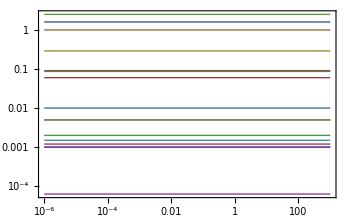

```mathematica
{concSol,fluxSol}=simulate[iABsalvage,{t,0,1000}];
plotSimulation[concSol]
```

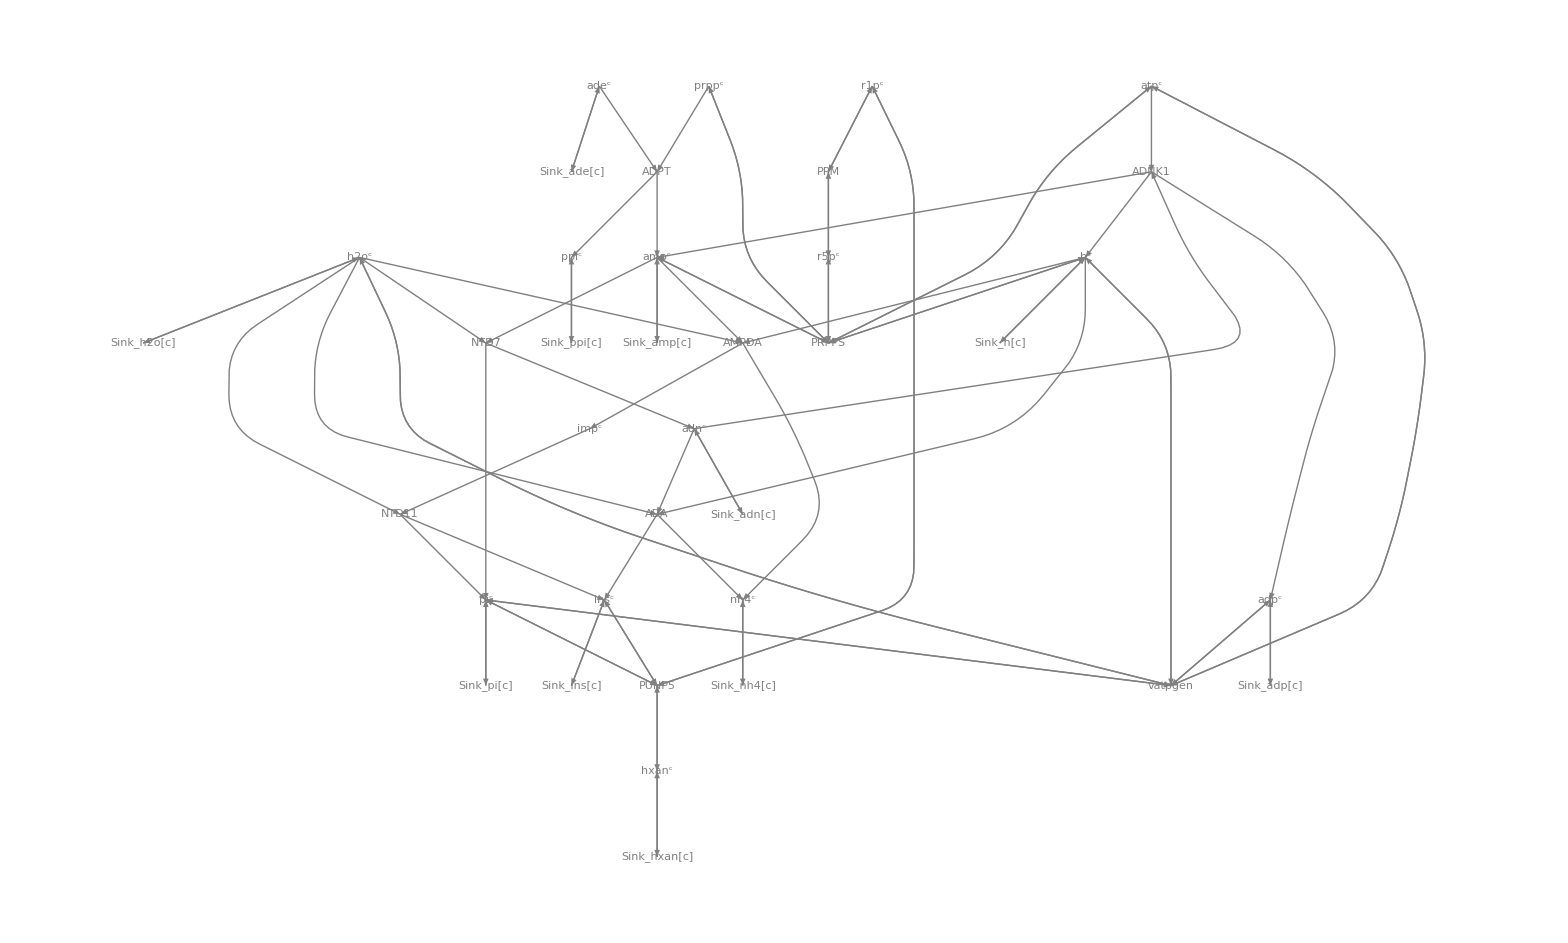

```mathematica
visualizePathways[reactions2bipartite[iABsalvage["Reactions"]],
DirectedEdges->True,PlotStyle->{GrayLevel[0.5],Arrowheads[.012]},
"MetaboliteRenderingFunction"->({Style[Text[StandardForm@#2,#1],
Background->Opacity[.6,White]]}&),"ReactionRenderingFunction"->({Style[Text[StandardForm@#2,#1],Larger,Background->Opacity[.6,LightGray]]}&),ImageSize->1600,MultiedgeStyle->None]
```

```mathematica
elementallyBalancedQ[iABsalvage]
stoichiometricallyConsistentQ[iABsalvage]
```

True

True

```mathematica
updateNotes[iABsalvage,defaultInitializationNotes[]<>"\n This model is a translation of the nucleotide salvage pathway model in 'Simulation of dynamic network state' in terms of the iAB-RBC-238 reconstruction by Aarash Bordbard."];
SetDirectory[NotebookDirectory[]];
Export["../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz",iABsalvage]
```

../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz

### Combinations (needs more work! fluxes are not in a steady-state)

```mathematica
SetDirectory[NotebookDirectory[]];
iABglycolysis=Import["../models/iAB-RBC-238/iAB-RBC-238-Glycolysis.m.gz"];
iABppp=Import["../models/iAB-RBC-238/iAB-RBC-238-PentosePhosphatePathway.m.gz"];
iABsalvage=Import["../models/iAB-RBC-238/iAB-RBC-238-NucleotideSalvagePathway.m.gz"];
```

```mathematica
combi=iABglycolysis∪iABppp∪iABsalvage;
```

```mathematica
combi["Constraints"]//Length
```

50

```mathematica
combi["Reactions"]
```

{(adn^c+h^c+h2o^c→ins^c+nh4^c)^ADA,(amp^c+atp^c⇌2 adp^c)^ADK1,(adn^c+atp^c→adp^c+amp^c+h^c)^ADNK1,(ade^c+prpp^c→amp^c+ppi^c)^ADPT,(amp^c+h^c+h2o^c→imp^c+nh4^c)^AMPDA,(atp^c+h2o^c⇌adp^c+h^c+pi^c)^ATP_hydrolysis,((2pg)^c⇌h2o^c+pep^c)^ENO,(fdp^c⇌dhap^c+g3p^c)^FBA,(g6p^c+nadp^c⇌(6pgl)^c+h^c+nadph^c)^G6PDH2r,(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD,((6pgc)^c+nadp^c→co2^c+nadph^c+(ru5p-D)^c)^GND,(gthox^c+h^c+nadph^c→2 gthrd^c+nadp^c)^GTHO,(2 gthrd^c+h2o2^c→gthox^c+2 h2o^c)^GTHP,(atp^c+(glc-D)^c→adp^c+g6p^c+h^c)^HEX1,((lac-L)^c+nad^c⇌h^c+nadh^c+pyr^c)^LDH_L,(nadh^c⇌h^c+nad^c)^NADH_oxidation,(h2o^c+imp^c→ins^c+pi^c)^NTD11,(amp^c+h2o^c→adn^c+pi^c)^NTD7,(atp^c+f6p^c→adp^c+fdp^c+h^c)^PFK,(g6p^c⇌f6p^c)^PGI,((3pg)^c+atp^c⇌(13dpg)^c+adp^c)^PGK,((6pgl)^c+h2o^c→(6pgc)^c+h^c)^PGL,((2pg)^c⇌(3pg)^c)^PGM,(r1p^c⇌r5p^c)^PPM,(atp^c+r5p^c⇌amp^c+h^c+prpp^c)^PRPPS,(ins^c+pi^c⇌hxan^c+r1p^c)^PUNP5,(adp^c+h^c+pep^c→atp^c+pyr^c)^PYK,((ru5p-D)^c⇌(xu5p-D)^c)^RPE,(r5p^c⇌(ru5p-D)^c)^RPI,(ade^c⇌∅)^Sink_ade[c],(adn^c⇌∅)^Sink_adn[c],(adp^c⇌∅)^Sink_adp[c],(amp^c⇌∅)^Sink_amp[c],(co2^c⇌∅)^Sink_co2[c],(f6p^c⇌∅)^Sink_f6p[c],(g3p^c⇌∅)^Sink_g3p[c],(g6p^c⇌∅)^Sink_g6p[c],((glc-D)^c⇌∅)^(Sink_glc-D[c]),(h2o2^c⇌∅)^Sink_h2o2[c],(h2o^c⇌∅)^Sink_h2o[c],(h^c⇌∅)^Sink_h[c],(hxan^c⇌∅)^Sink_hxan[c],(ins^c⇌∅)^Sink_ins[c],((lac-L)^c⇌∅)^(Sink_lac-L[c]),(nh4^c⇌∅)^Sink_nh4[c],(pi^c⇌∅)^Sink_pi[c],(ppi^c⇌∅)^Sink_ppi[c],(pyr^c⇌∅)^Sink_pyr[c],(g3p^c+s7p^c⇌e4p^c+f6p^c)^TALA,(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1,(e4p^c+(xu5p-D)^c⇌f6p^c+g3p^c)^TKT2,(dhap^c⇌g3p^c)^TPI,(adp^c+h^c+pi^c⇌atp^c+h2o^c)^vatpgen}

```mathematica
{concSol,fluxSol}=simulate[combi];
```

NDSolve::ndsz: At t == 4.3373, step size is effectively zero; singularity or stiff system suspected.

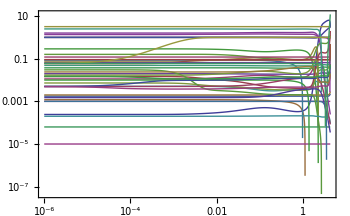

```mathematica
plotSimulation[concSol]
```

## Hemoglobin

```mathematica
SetDirectory[NotebookDirectory[]];
rbc=Import["../models/iAB-RBC-238/iAB-RBC-238.m.gz"];
```

### Adair

```mathematica
init=protein["Hb_Oxy","c"];
oxygenationHb=Table[
prod=bind[init,MASSToolbox`MASS`metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
oxygenationHb
```

{(o2^c+Hb_Oxy^c⇌Hb_Oxy^c | o2^c)^(protein_Hb_Oxy & o2[c] + o2[c]),(Hb_Oxy^c | o2^c+o2^c⇌Hb_Oxy^c | 2 o2^c)^(protein_Hb_Oxy & 2 o2[c] + o2[c]),(Hb_Oxy^c | 2 o2^c+o2^c⇌Hb_Oxy^c | 3 o2^c)^(protein_Hb_Oxy & 3 o2[c] + o2[c]),(Hb_Oxy^c | 3 o2^c+o2^c⇌Hb_Oxy^c | 4 o2^c)^(protein_Hb_Oxy & 4 o2[c] + o2[c])}

```mathematica
adairHb=constructModel[oxygenationHb];
```

### MWC

```mathematica
init=protein["Hb_Oxy","c"];
oxygenationHb=Table[
prod=bind[init,MASSToolbox`MASS`metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
init=protein["Hb_Deoxy","c"];
oxygenationDHb=Table[
prod=bind[init,MASSToolbox`MASS`metabolite["o2", "c"]];
rxn=r[ToString[prod]<>" + " <>ToString[o2^c],{init,o2^c},{prod},{1,1,1}];
init=prod;
rxn
,{i,1,4}];
```

```mathematica
transition=Table[
substr=complex[protein["Hb_Deoxy","c"],Sequence@@Table[o2^c,{i}]];
prod=complex[protein["Hb_Oxy","c"],Sequence@@Table[o2^c,{i}]];
rxn=r[ToString[substr]<>" <=> " <>ToString[prod],{substr},{prod},{1,1}];
(*rxn=r["T2R_"<>ToString[i],{substr},{prod},{1,1}];*)
init=prod;
rxn
,{i,1,4}];
```

```mathematica
hb=constructModel[Join[oxygenationHb,oxygenationDHb,transition]];
```

```mathematica
hb
```

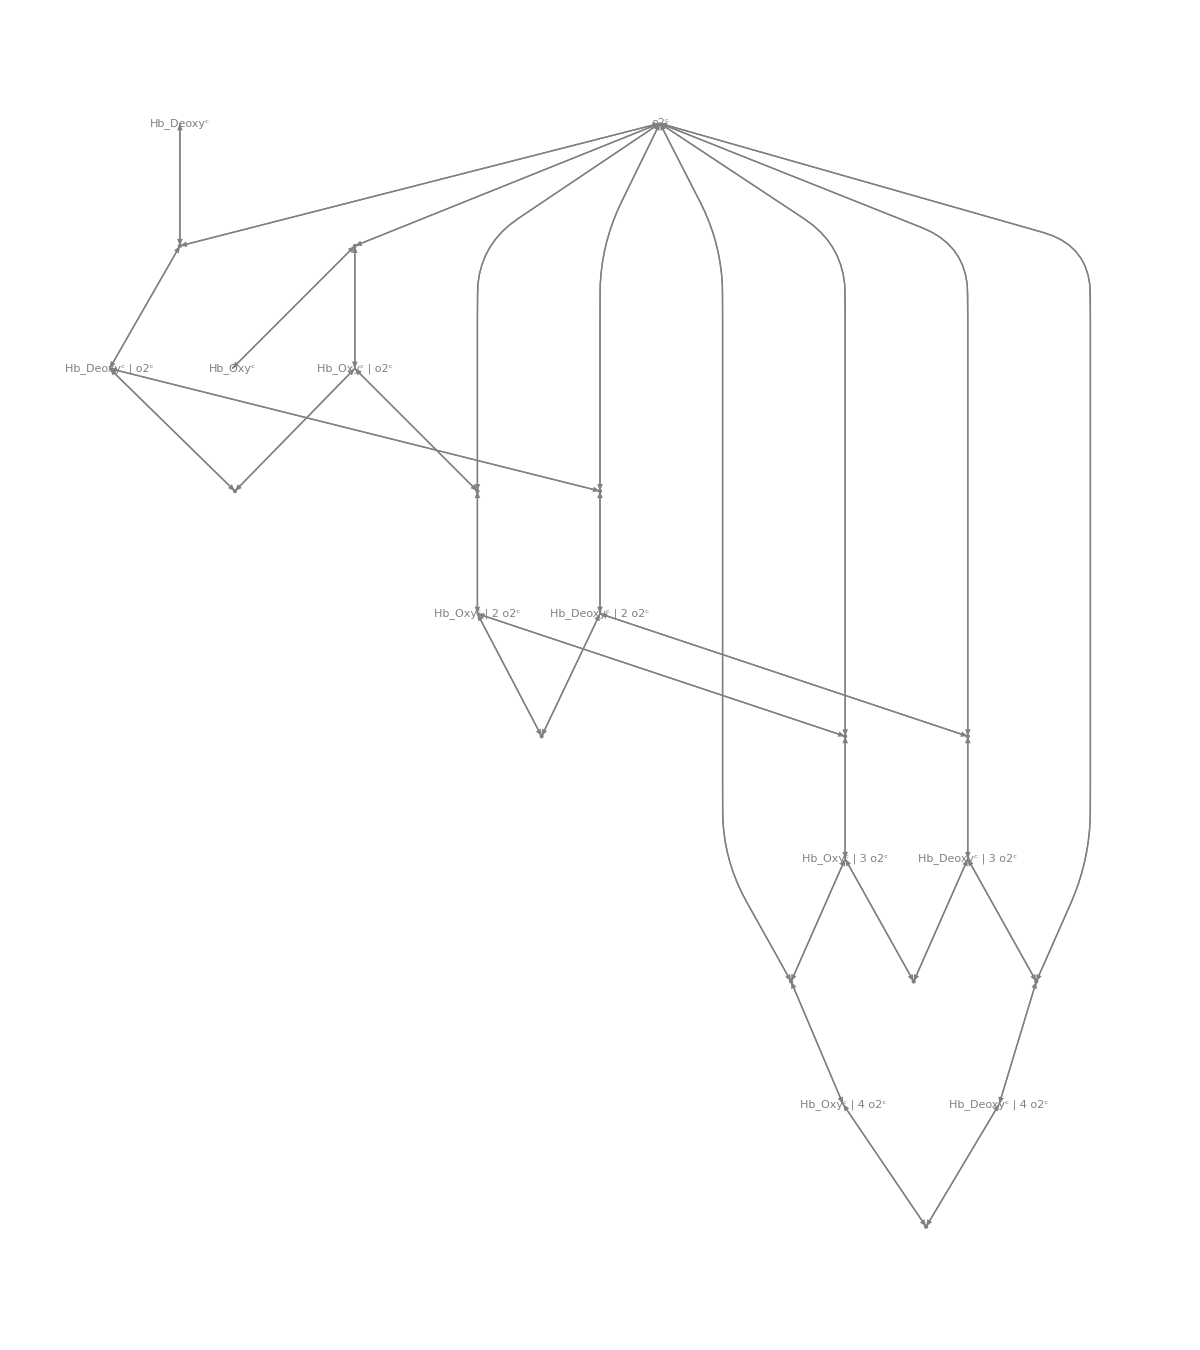

```mathematica
visualizePathways[hb,"MetaboliteRenderingFunction"->(Text[StandardForm[#2],#1]&),"ReactionRenderingFunction"->(Point[#1]&),ImageSize->1200]
```